```mathematica
NS["silence_bias","C:\\Users\\pglpm\\repositories\\maxNt\\scripts"]
```

```mathematica
rates=Flatten@Import["rates.csv"][[2;;]]
```

{0.0138157,0.0079111,0.00244229,0.00916098,0.00652714,0.00248539,0.00452781,0.0836388,0.00219327,0.00504261,0.00227708,0.0601354,0.0117876,0.00307202,0.00606741,0.0893135,0.0123216,0.00416865,0.008038,0.00872999,0.00408245,0.00701081,0.0491547,0.00439612,0.00507852,0.00300258,0.0220452,0.00402738,0.00264581,0.00381668,0.00181974,0.00473373,0.00571783,0.00967099,0.00209031,0.00290441,0.00566755,0.0288142,0.00646009,0.00459007,0.0253591,0.0239488,0.0205679,0.0147351,0.00108706,0.0106407,0.00117565,0.000792547,0.00191313,0.0577745,0.0034647,0.014297,0.0277583,0.0322646,0.00382625,0.00249975,0.00866773,0.00644812,0.00219088,0.0067977,0.00604347,0.00382386,0.00392921,0.00274398,0.00318934}

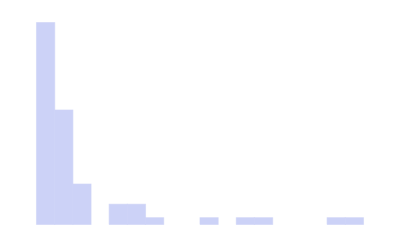

```mathematica
Histogram[rates,"FreedmanDiaconis","PDF",PlotRange->All]
```

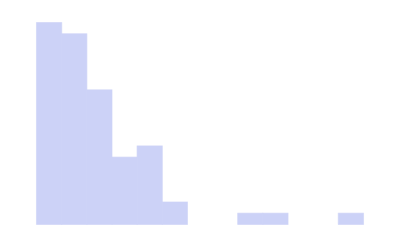

```mathematica
Histogram[1/rates,"FreedmanDiaconis","PDF",PlotRange->All]
```

```mathematica
apps=Import["firstapps.csv"][[2;;]]
```

{{3,3},{4,4},{7,5},{17,6},{18,7},{22,8},{23,9},{26,10},{27,11},{30,12},{31,14},{35,15},{37,16},{38,18},{39,20},{41,21},{43,23},{44,24},{48,25},{71,26},{72,27},{75,29},{76,30},{80,31},{82,32},{86,33},{87,34},{92,35},{117,36},{118,37},{129,38},{159,39},{175,40},{203,41},{219,42},{221,43},{222,44},{274,45},{283,46},{303,47},{384,48},{419,49},{531,50},{588,51},{636,52},{640,53},{658,54},{733,55},{767,56},{795,57},{796,58},{928,59},{1134,60},{2516,61},{4859,62},{4980,63},{5630,64},{5678,65}}

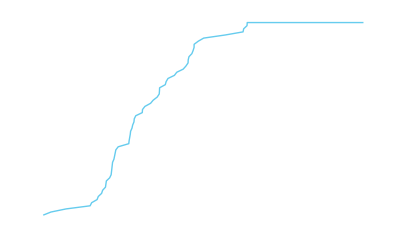

```mathematica
ListLogLinearPlot[Append[{417641,65}]@apps,Joined->True,PlotRange->All,FrameLabel->{bin,"# of discovered neurons"},ImageSize->a4shortside]
```

```mathematica
expng["newneurons_vs_time_log",%]
```

newneurons_vs_time_log.png

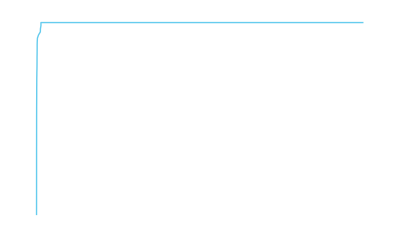

```mathematica
ListPlot[Append[{417641,65}]@apps,Joined->True,PlotRange->All,FrameLabel->{bin,"# of discovered neurons"},ImageSize->a4shortside]
```

```mathematica
expng["newneurons_vs_time",%]
```

newneurons_vs_time.png

```mathematica
apps2=Import["timesn2.csv"][[2;;]];
```

```mathematica
Dimensions[apps2]
```

{210069,2}

```mathematica
apps2[[1;;10]]
```

{{3,3},{4,4},{5,4},{7,5},{17,6},{18,7},{22,8},{23,9},{26,10},{27,11}}

```mathematica
Max[apps2[[;;,2]]]
```

65

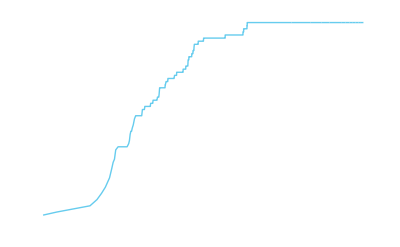

```mathematica
ListLogLinearPlot[apps2[[;;;;Round[Length[apps2]/100000]]],Joined->True,PlotRange->{{All,417641},All}]
```

```mathematica
apps=Import["apparitions.csv"][[2;;]]
```

{{17,211184.,417268},{4980,205406.,417573},{795,188964.,417593},{796,167728.,412953},{23,189905.,416942},{658,159481.,416806},{4859,206888.,417327},{35,200671.,417600},{1134,180516.,416792},{30,199031.,417427},{118,201236.,417386},{39,196577.,417603},{159,218376.,417295},{222,207911.,416231},{303,256324.,417295},{31,198675.,417593},{43,201235.,417226},{76,188310.,416682},{636,188983.,417254},{175,220407.,416624},{928,176464.,417258},{38,197079.,417346},{27,187455.,417641},{71,205262.,417170},{640,191190.,417640},{203,199205.,415201},{38,194984.,417635},{221,212135.,416585},{72,217258.,413894},{117,204575.,416972},{531,165915.,404739},{75,200128.,413420},{384,208021.,417271},{733,204293.,417564},{26,199910.,415267},{18,199566.,417221},{80,217993.,417460},{588,224554.,417618},{48,207482.,417295},{274,181900.,415951},{7,203732.,417578},{37,206373.,417507},{3,213010.,417400},{22,201228.,417639},{283,197680.,416465},{31,208431.,417459},{767,173533.,415474},{5630,168314.,410840},{2516,201294.,417457},{3,206797.,417551},{5678,215238.,417513},{3,191767.,417606},{39,203740.,417582},{82,199432.,417539},{419,191313.,415245},{4,241171.,415953},{43,205884.,417232},{129,222322.,417241},{41,188541.,412986},{44,224870.,417604},{86,206133.,417533},{87,176966.,416837},{75,215033.,415938},{92,200767.,417277},{219,210222.,417597}}

```mathematica
sapps=SortBy[apps,First]
```

{{3,191767.,417606},{3,206797.,417551},{3,213010.,417400},{4,241171.,415953},{7,203732.,417578},{17,211184.,417268},{18,199566.,417221},{22,201228.,417639},{23,189905.,416942},{26,199910.,415267},{27,187455.,417641},{30,199031.,417427},{31,198675.,417593},{31,208431.,417459},{35,200671.,417600},{37,206373.,417507},{38,194984.,417635},{38,197079.,417346},{39,196577.,417603},{39,203740.,417582},{41,188541.,412986},{43,201235.,417226},{43,205884.,417232},{44,224870.,417604},{48,207482.,417295},{71,205262.,417170},{72,217258.,413894},{75,200128.,413420},{75,215033.,415938},{76,188310.,416682},{80,217993.,417460},{82,199432.,417539},{86,206133.,417533},{87,176966.,416837},{92,200767.,417277},{117,204575.,416972},{118,201236.,417386},{129,222322.,417241},{159,218376.,417295},{175,220407.,416624},{203,199205.,415201},{219,210222.,417597},{221,212135.,416585},{222,207911.,416231},{274,181900.,415951},{283,197680.,416465},{303,256324.,417295},{384,208021.,417271},{419,191313.,415245},{531,165915.,404739},{588,224554.,417618},{636,188983.,417254},{640,191190.,417640},{658,159481.,416806},{733,204293.,417564},{767,173533.,415474},{795,188964.,417593},{796,167728.,412953},{928,176464.,417258},{1134,180516.,416792},{2516,201294.,417457},{4859,206888.,417327},{4980,205406.,417573},{5630,168314.,410840},{5678,215238.,417513}}

```mathematica
ran=Range[65];
```

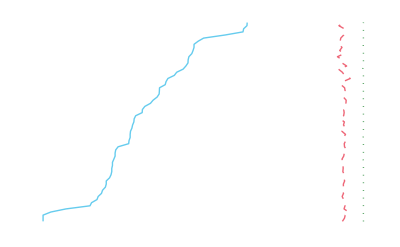

```mathematica
ListLogLinearPlot[{T@{sapps[[;;,1]],ran},T@{sapps[[;;,2]],ran},T@{sapps[[;;,3]],ran}},Joined->True,PlotRange->{{All,417641},All},FrameLabel->{bin,"# of discovered neurons"},ImageSize->a4shortside]
```

```mathematica
expng["newneurons_vs_time",%]
```

newneurons_vs_time.png

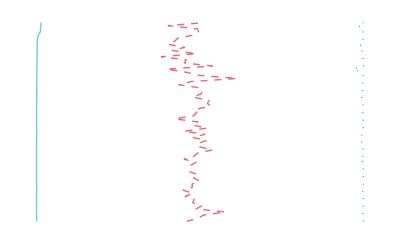

```mathematica
ListPlot[{T@{sapps[[;;,1]],ran},T@{sapps[[;;,2]],ran},T@{sapps[[;;,3]],ran}},Joined->True,PlotRange->{{All,417641},All},FrameLabel->{bin,"# of discovered neurons"},ImageSize->a4shortside]
```